# Ajuste de modelos con base arbitraria II

### Carlos Manuel Rodríguez Martínez 18/Mar/2020

Definición de función objetivo

```mathematica
TargetFunction[x_]:=Sin[x];
```

Creación del conjunto de entrenamiento y de prueba.

```mathematica
{a,b}={0,10};
δ = (b-a)/10;
baseFunction = Table[{x,TargetFunction[x]},{x,a,b,0.25*δ}];
trainingSet = Table[{x,TargetFunction[x]+RandomVariate[NormalDistribution[0,0.1]]},{x,a,b,δ}];
validationSet = Table[{x,TargetFunction[x]+RandomVariate[NormalDistribution[0,0.1]]},{x,Sort[RandomReal[{a,b},10]]}];
```

Gráfica del conjunto de entrenamiento y conjunto de prueba.

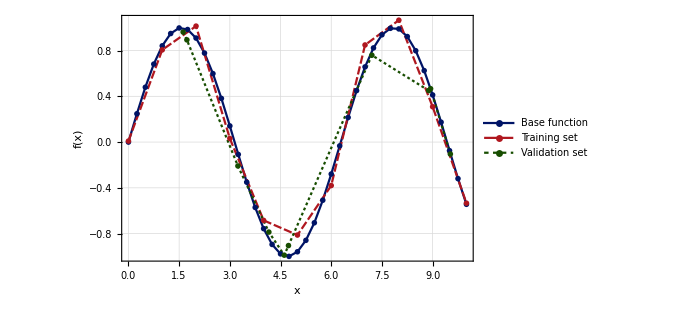

```mathematica
ListLinePlot[
{baseFunction,trainingSet,validationSet},
PlotLegends->{"Base function","Training set","Validation set"},
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15], Style["f(x)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0., 0.08, 0.4],RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500
]
```

Defininción de función de error y E_RMS

```mathematica
PolynomialBase[x_,n_]:=Table[If[i==0,1,x^i],{i,0,n-1}];
GaussianBase[x_,n_, σ_ : 1]:=Block[{δ = (b-a)/n},Table[Exp[- (x-(a+δ i))^2/(2 σ^2)],{i,0,n-1}]];
SigmoidBase[x_,n_, σ_ : 1]:=Block[{δ = (b-a)/n},Table[LogisticSigmoid[(x-(a+δ i))/σ],{i,0,n-1}]];

ExpandBase[x_,w_,baseFunction_]:=w.baseFunction[x,Length[w]];
FitBase[data_,n_,baseFunction_]:=Module[{x,weights},
weights = Table[ToExpression[StringJoin["w",ToString[i]]],{i,0,n-1}];

weights/.FindFit[data,ExpandBase[x,weights,baseFunction],weights,x]
];

FitExpressionWithBase[data_,x_,n_,baseFunction_]:=ExpandBase[x,FitBase[data,n,baseFunction],baseFunction];
```

### Gráficas de las bases

Polinomial

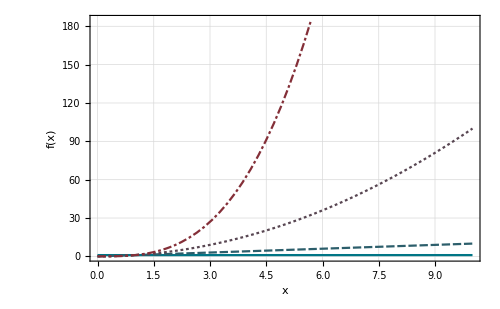

```mathematica
Plot[
Evaluate@PolynomialBase[x,4],
{x,a,b},
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15], Style["f(x)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->Table[Blend[{RGBColor[0., 0.46, 0.52],RGBColor[0.689993, 0.089999, 0.119999]},x],{x,0,1,1/4}],
Frame->True,
ImageSize->500
]
```

Gaussiana

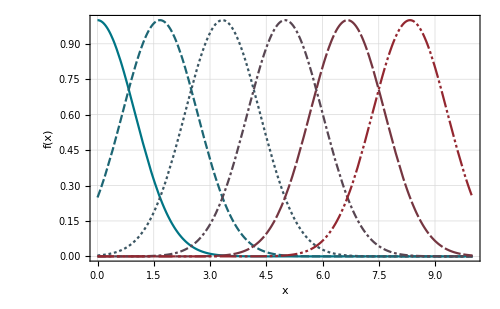

```mathematica
Plot[
Evaluate@GaussianBase[x,6],
{x,a,b},
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15], Style["f(x)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->Table[Blend[{RGBColor[0., 0.46, 0.52],RGBColor[0.689993, 0.089999, 0.119999]},x],{x,0,1,1/6}],
Frame->True,
ImageSize->500
]
```

Sigmoide

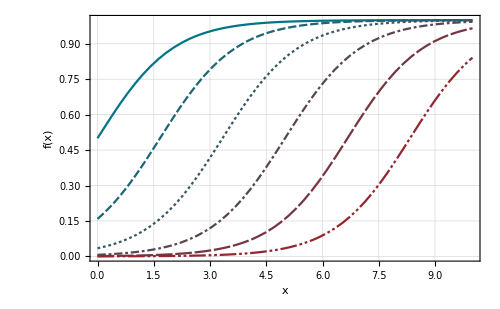

```mathematica
Plot[
Evaluate@SigmoidBase[x,6],
{x,a,b},
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15], Style["f(x)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->Table[Blend[{RGBColor[0., 0.46, 0.52],RGBColor[0.689993, 0.089999, 0.119999]},x],{x,0,1,1/6}],
Frame->True,
ImageSize->500
]
```

```mathematica
ExpandBase[x,{w1,w2,w3},PolynomialBase]
```

w1+w2 x+w3 x^2

```mathematica
ExpandBase[x,{w1,w2,w3},GaussianBase]
```

ⅇ^(-x^2/2) w1+ⅇ^(-1/2 (-10/3+x)^2) w2+ⅇ^(-1/2 (-20/3+x)^2) w3

```mathematica
ExpandBase[x,{w1,w2,w3},SigmoidBase]
```

w3 LogisticSigmoid[-20/3+x]+w2 LogisticSigmoid[-10/3+x]+w1 LogisticSigmoid[x]

```mathematica
FitBase[trainingSet,5,GaussianBase]
```

{-0.170677,1.16567,-0.843545,-0.326515,0.978348}

```mathematica
FitExpressionWithBase[trainingSet,x,5,PolynomialBase]
```

-0.12853+1.97516 x-1.10652 x^2+0.186066 x^3-0.00958075 x^4

```mathematica
FitExpressionWithBase[trainingSet,x,5,GaussianBase]
```

0.978348 ⅇ^(-1/2 (-8+x)^2)-0.326515 ⅇ^(-1/2 (-6+x)^2)-0.843545 ⅇ^(-1/2 (-4+x)^2)+1.16567 ⅇ^(-1/2 (-2+x)^2)-0.170677 ⅇ^(-x^2/2)

```mathematica
FitExpressionWithBase[trainingSet,x,5,SigmoidBase]
```

-6.19253 LogisticSigmoid[-8+x]+11.7708 LogisticSigmoid[-6+x]-10.2758 LogisticSigmoid[-4+x]+3.85335 LogisticSigmoid[-2+x]-0.14393 LogisticSigmoid[x]

### Ajuste con el método Moore-Penrose pseudo-inverse

```mathematica
PhiDesignMatrix[data_,n_,baseFunction_]:=Module[{base,x},
base = baseFunction[x,n];
Map[N[base/.{x->#}]&,data]
];
MoorePenrosePseudoInverse[m_]:=Quiet@Inverse[Transpose[m].m].Transpose[m];
FitWithMPPseudoInverse[data_,n_,baseFunction_]:=Block[{ϕ},
ϕ = PhiDesignMatrix[data[[All,1]],n,baseFunction];
MoorePenrosePseudoInverse[ϕ].data[[All,2]]
];
FitMPExpressionWithBase[data_,x_,n_,baseFunction_]:=ExpandBase[x,FitWithMPPseudoInverse[data,n,baseFunction],baseFunction];

EstimatePrecisionβ[data_,n_,baseFunction_]:=Block[{wML},
wML = FitWithMPPseudoInverse[data,n,baseFunction];
EstimatePrecisionβ[data,n,baseFunction,wML]
];
EstimatePrecisionβ[data_,n_,baseFunction_,weights_]:=Block[{wML},
Total[(data[[All,2]]-Map[weights.# &,PhiDesignMatrix[data[[All,1]],n,baseFunction]])^2]/Length[data]
];
Error[data_,n_,baseFunction_,λ_,weights_]:=1/2 Total[(data[[All,2]]-Map[weights.# &,PhiDesignMatrix[data[[All,1]],n,baseFunction]])^2]+λ/2 weights.weights;
Error[data_,n_,baseFunction_,λ_]:=Block[{weights},
weights = FitWithMPPseudoInverse[data,n,baseFunction];
Error[data,n,baseFunction,λ,weights]
];
ERMS[data_,n_,baseFunction_,λ_,weights_]:=√((2 Error[data,n,baseFunction,λ,weights])/Length[data]);
ERMS[data_,n_,baseFunction_,λ_]:=√((2 Error[data,n,baseFunction,λ])/Length[data]);
```

```mathematica
wML = FitWithMPPseudoInverse[trainingSet,5,GaussianBase]
```

{-0.170677,1.16567,-0.843545,-0.326515,0.978348}

```mathematica
EstimatePrecisionβ[trainingSet,5,GaussianBase,wML]
```

0.0847516

```mathematica
Error[trainingSet,5,GaussianBase,0,wML]
```

0.466134

Ejemplos de ajuste de los datos con diferentes bases con M = 5

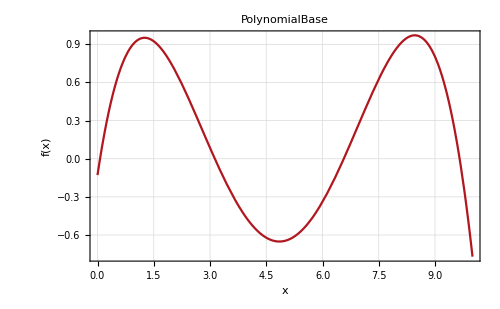
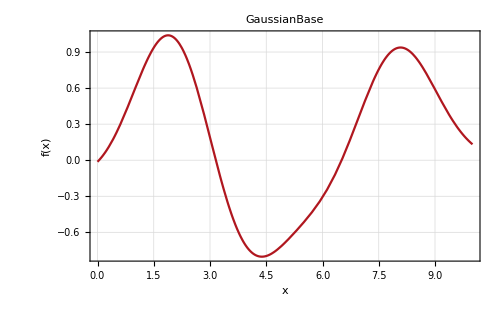
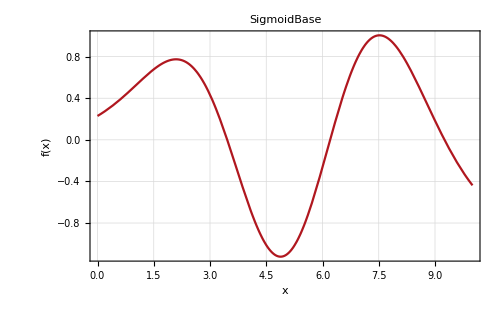

```mathematica
Map[
Plot[
FitMPExpressionWithBase[trainingSet,x,5,#],
{x,a,b},
PlotLabel->#,
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15], Style["f(x)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999]},
Frame->True,
ImageSize->500
]&,
{PolynomialBase,GaussianBase,SigmoidBase}
]
```

Gráficas de los ajustes junto con los polinomios base

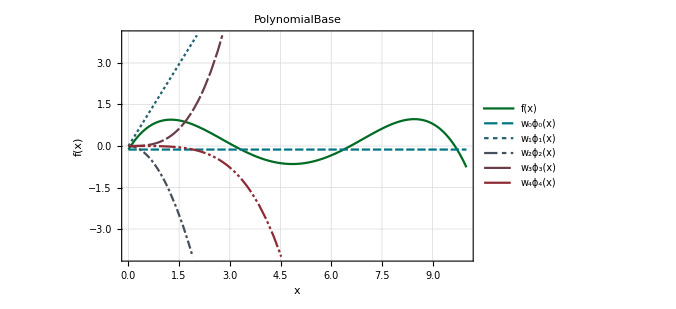
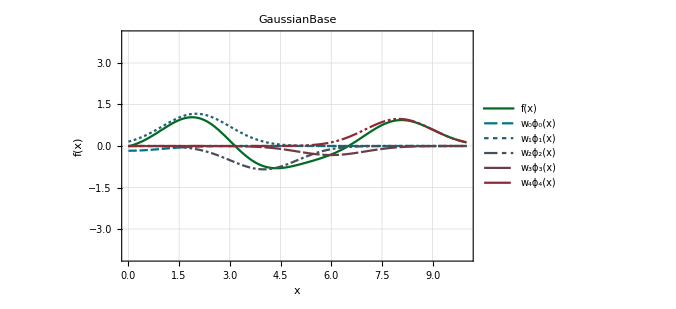
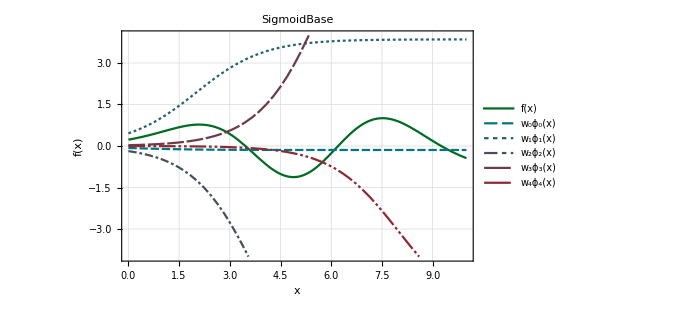

```mathematica
Map[
Plot[
Evaluate@Prepend[FitWithMPPseudoInverse[trainingSet,5,#]*#[x,5],FitMPExpressionWithBase[trainingSet,x,5,#]],
{x,a,b},
PlotLabel->#,
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15], Style["f(x)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->Prepend[Table[Blend[{RGBColor[0., 0.46, 0.52],RGBColor[0.689993, 0.089999, 0.119999]},x],{x,0,1,1/5}],RGBColor[0., 0.42, 0.14]],
Frame->True,
ImageSize->500,
PlotLegends->{"f(x)","w_0ϕ_0(x)","w_1ϕ_1(x)","w_2ϕ_2(x)","w_3ϕ_3(x)","w_4ϕ_4(x)"},
PlotRange->{{a,b},{-4,4}}
]&,
{PolynomialBase,GaussianBase,SigmoidBase}
]
```

### Comparación del error E_RMS para el conjunto de entrenamiento y de prueba.

#### Base Polinomial

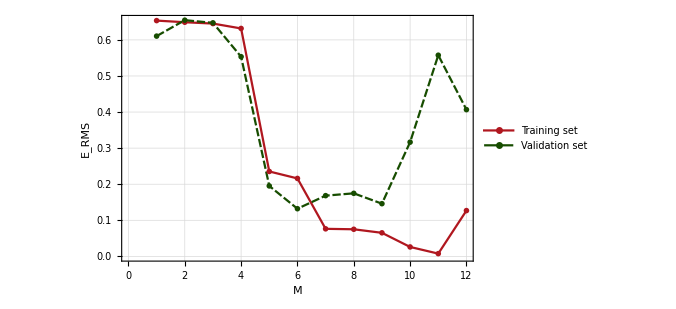

```mathematica
errorVsMTraining = Table[{M,ERMS[trainingSet,M,PolynomialBase,0,FitWithMPPseudoInverse[trainingSet,M,PolynomialBase]]},{M,1,12}];
errorVsMValidation = Table[{M,ERMS[validationSet,M,PolynomialBase,0,FitWithMPPseudoInverse[trainingSet,M,PolynomialBase]]},{M,1,12}];

ListLinePlot[
{errorVsMTraining,errorVsMValidation},
PlotLegends->{"Training set","Validation set"},
PlotTheme->"Monochrome",
FrameLabel->{Style["M",15], Style["E_RMS",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500
]
```

El valor de M que minimiza la suma de los errores en ambos conjuntos es M=9

```mathematica
MinimalBy[
Table[
{First[errorVsMTraining[[i]]],Last[errorVsMTraining[[i]]]+Last[errorVsMValidation[[i]]]},
{i,1,Length[errorVsMTraining]}],
Last
]
```

{{9,0.211371}}

#### Base Gaussiana

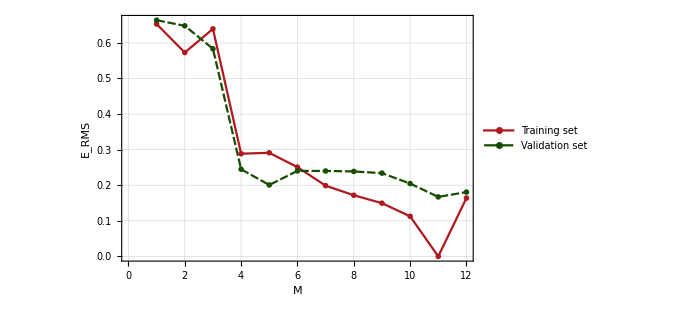

```mathematica
errorVsMTraining = Table[{M,ERMS[trainingSet,M,GaussianBase,0,FitWithMPPseudoInverse[trainingSet,M,GaussianBase]]},{M,1,12}];
errorVsMValidation = Table[{M,ERMS[validationSet,M,GaussianBase,0,FitWithMPPseudoInverse[trainingSet,M,GaussianBase]]},{M,1,12}];

ListLinePlot[
{errorVsMTraining,errorVsMValidation},
PlotLegends->{"Training set","Validation set"},
PlotTheme->"Monochrome",
FrameLabel->{Style["M",15], Style["E_RMS",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500
]
```

El valor de M que minimiza la suma de los errores en ambos conjuntos es M=11

```mathematica
MinimalBy[
Table[
{First[errorVsMTraining[[i]]],Last[errorVsMTraining[[i]]]+Last[errorVsMValidation[[i]]]},
{i,1,Length[errorVsMTraining]}],
Last
]
```

{{11,0.16715}}

#### Base Sigmoide

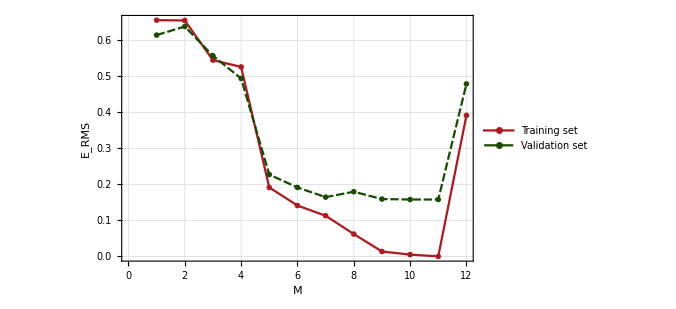

```mathematica
errorVsMTraining = Table[{M,ERMS[trainingSet,M,SigmoidBase,0,FitWithMPPseudoInverse[trainingSet,M,SigmoidBase]]},{M,1,12}];
errorVsMValidation = Table[{M,ERMS[validationSet,M,SigmoidBase,0,FitWithMPPseudoInverse[trainingSet,M,SigmoidBase]]},{M,1,12}];

ListLinePlot[
{errorVsMTraining,errorVsMValidation},
PlotLegends->{"Training set","Validation set"},
PlotTheme->"Monochrome",
FrameLabel->{Style["M",15], Style["E_RMS",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500
]
```

El valor de M que minimiza la suma de los errores en ambos conjuntos es M=11

```mathematica
MinimalBy[
Table[
{First[errorVsMTraining[[i]]],Last[errorVsMTraining[[i]]]+Last[errorVsMValidation[[i]]]},
{i,1,Length[errorVsMTraining]}],
Last
]
```

{{11,0.157925}}

### Medición de precisión β

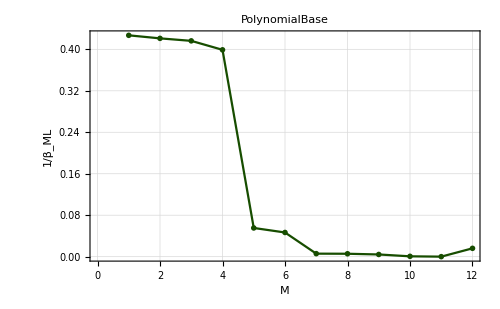
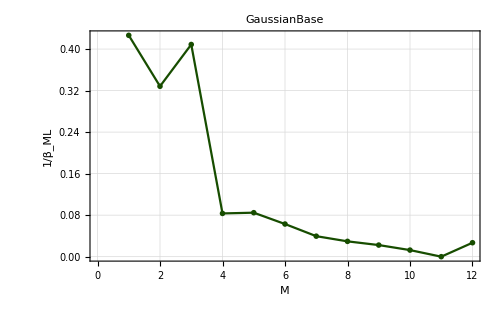
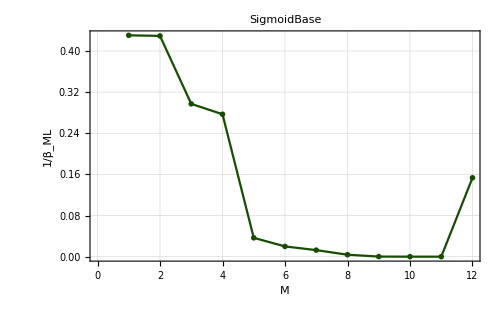

```mathematica
Map[
ListLinePlot[
Table[{M,EstimatePrecisionβ[trainingSet,M,#]},{M,1,12}],
PlotTheme->"Monochrome",
FrameLabel->{Style["M",15], Style["1/β_ML",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500,
PlotLabel->#
]&,
{PolynomialBase,GaussianBase,SigmoidBase}
]
```